```mathematica
Clear["Global`*"]
```

```mathematica
J1=2;
E0=-3*B/2;
E1=(-B-J2)/2;
E2=(B-J2)/2;
E3=-B/2+1/4*(J2-Sqrt[J2^2+8*J1^2]);
E4=B/2+1/4*(J2-Sqrt[J2^2+8*J1^2]);
E5=-B/2+1/4*(J2+Sqrt[J2^2+8*J1^2]);
E6=B/2+1/4*(J2+Sqrt[J2^2+8*J1^2]);
E7=3*B/2;
a3=a4=(-J2-Sqrt[J2^2+8*J1^2])/(2*J1);
a5=a6=Sqrt[2+a4^2];
N3=N4=Sqrt[2+a3^2];
N5=N6=Sqrt[2+a6^2];
T=0.05;
u=Exp[-E0/T]+((a3^2)*Exp[-E3/T]/(N3^2))+(a5^2)*Exp[-E5/T]/(N5^2);
v=Exp[-E7/T]+((a4^2)*Exp[-E4/T]/(N4^2))+(a6^2)*Exp[-E6/T]/(N6^2);
w=-1/2*Exp[-E1/T]-1/2*Exp[-E2/T]+(Exp[-E3/T]/(N3^2))+(Exp[-E4/T]/(N4^2))+(Exp[-E5/T]/(N5^2))+(Exp[-E6/T]/(N6^2));
Z=Exp[3 B/(2 T)]+Exp[(B+J2)/(2 T)]+Exp[(-B+J2)/(2 T)]+Exp[(2 B-(J2-Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[-(2 B+(J2-Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[(2 B-(J2+Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[-(2 B+(J2+Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[-3 B/(2 T)];
C1=2*(Abs[w]-Sqrt[u*v])/Z;
C2=Max[C1,0];
J2=0;
t1=Table[{B,C2},{B,-8,8,0.2}];
J2=2;
t2=Table[{B,C2},{B,-8,8,0.2}];
J2=4;
t3=Table[{B,C2},{B,-8,8,0.2}];
J2=6;
t4=Table[{B,C2},{B,-8,8,0.2}];
```

```mathematica
p3=ListLinePlot[{t1,t2,t3,t4},ImageSize->300,ImagePadding->20,Frame->{{True,False},{True,True}}
,AxesOrigin->{-8,0},FrameTicks->{{Automatic,None},{{-8,-6,-4,-2,0,2,4,6,8},{-8,-6,-4,-2,0,2,4,6,8}}},PlotMarkers->{"○","●","△","□"},PlotStyle->{{Black,Thickness[0.0002]},{Black,Thickness[0.0002]},{Black,Thickness[0.0002]},{Black,Thickness[0.0002]}}]
```

-Graphics-

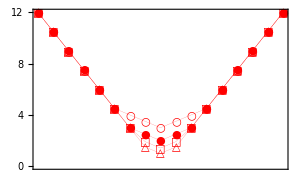

```mathematica
p4=ListLinePlot[{{{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-3},{-1,(-2-4 √2)/4},{0,-√2},{1,(-2-4 √2)/4},{2,-3},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}},{{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-3},{-1,-3/2},{0,-1},{1,-3/2},{2,-3},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}},{{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-3},{-1,-5/2},{0,-2},{1,-5/2},{2,-3},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}},{{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-4},{-1,-7/2},{0,-3},{1,-7/2},{2,-4},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}}},ImageSize->300,ImagePadding->20,Frame->{{False,True},{False,False}},
AxesOrigin->{-8,0},FrameTicks->{{None,{0,-2,-4,-6,-8,-10,-12}},{None,None}},ScalingFunctions->{Identity,"Reverse"},PlotMarkers->{"□","△","●","○"},PlotStyle->{{Red,Thickness[0.0002]},{Red,Thickness[0.0002]},{Red,Thickness[0.0002]},{Red,Thickness[0.0002]}}]
```

```mathematica
Overlay[{p3,p4}]
```

-Graphics--Graphics-